```mathematica
β[ω_,δ_,t_,ϵ_]:={{ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{-t,ⅈ δ-ϵ+ω,-t,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,-t,ⅈ δ-ϵ+ω,-t,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,-t,ⅈ δ-ϵ+ω,-t},{0,0,0,0,0,-t,ⅈ δ-ϵ+ω}}
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.001,1,0]],A:=Inverse[β[ω,0.001,1,0]],B:=Inverse[β[ω,0.001,1,0]],T1:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}},T2:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}},Do[J=Inverse[IdentityMatrix[7]-A.T1.Inverse[IdentityMatrix[7]-B.T2.J.T2].B.T1].A,4000];J=J]
```

```mathematica
T2[t_]:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}
```

```mathematica
T1[t_]:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}}
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,0.001,1,0]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[1].LEFT[ω,δ,t,ϵ].T2[1]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[1].LEFT[ω,δ,t,ϵ].T2[1]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SL[ω,δ,t,ϵ].T1[1].SR[ω,δ,t,ϵ].T1[1]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].SL[ω,δ,t,ϵ].T1[1]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[1].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T1[1].grr[ω,δ,t,ϵ].T1[1]-T1[1].GNON[ω,δ,t,ϵ].T1[1].GNON[ω,δ,t,ϵ]]
```

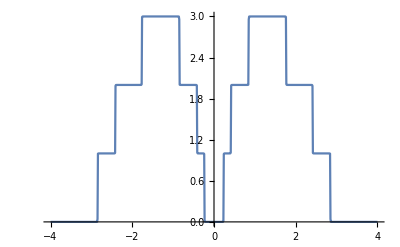

```mathematica
ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
Clear[Sl11,Sl12,Sl13,Sl14,Sl15,Sl16,Sl17,Sl18,Il1,Ir1,gdd1,grr1,Gnonlocal1,GNON1,Λ];X[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:=Inverse[{{ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{-t,ⅈ δ-ϵ2+ω,-t,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,-t,ⅈ δ-ϵ3+ω,-t,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,-t,ⅈ δ-ϵ2+ω,-t},{0,0,0,0,0,-t,ⅈ δ-ϵ+ω}}];
```

```mathematica
Λ[ω_,δ_,t_,ϵ_,ϵ2_,ϵ3_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},Sl11:=Inverse[IdentityMatrix[7]-g.T1[1].SL[ω,δ,t,ϵ].T1[1]].g;
Sl12:=Inverse[IdentityMatrix[7]-X[ω,δ,t,ϵ,ϵ2,ϵ3].T2[1].Sl11.T2[1]].X[ω,δ,t,ϵ,ϵ2,ϵ3];
Il1:=Inverse[IdentityMatrix[7]-Sl12.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl12;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[1].Sl12.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
A53:=A53=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis53.csv"]
```

```mathematica
f53[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A53[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A53[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
ρ53=Table[{b,a,f53[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00213145},{0.05,-1.,0.00213407},{0.1,-1.,0.00212989},{0.15,-1.,0.002212},{0.2,-1.,0.00243461},{0.25,-1.,0.00297762},{0.3,-1.,0.00351485},{0.35,-1.,0.00375934},{0.4,-1.,0.00402792},{0.45,-1.,0.00431159},22,{1.6,-1.,0.00925203},{1.65,-1.,0.00949365},{1.7,-1.,0.0097326},{1.75,-1.,0.00996858},{1.8,-1.,0.0102014},{1.85,-1.,0.0104308},{1.9,-1.,0.0106562},{1.95,-1.,0.010867},{2.,-1.,0.0110743}},39,{1}}
 |  |  |  |

```mathematica
{Extract[ρ53⟦Position[Table[{i,{Min/@Transpose[ρ53⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ53⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ53[[Position[Table[{i,{Min/@Transpose[ρ53[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ53[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ53[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ53⟦Position[Table[{i,{Min/@Transpose[ρ53⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ53⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ53[[Position[Table[{i,{Min/@Transpose[ρ53[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ53[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ53[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ53⟦Position[Table[{i,{Min/@Transpose[ρ53⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ53⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ53[[Position[Table[{i,{Min/@Transpose[ρ53[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ53[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ53[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]}
```

{{0.45},{0.15},{0.0000337684}}

```mathematica
A54:=A54=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis54.csv"]
```

```mathematica
f54[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A54[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A54[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
ρ54=Table[{b,a,f54[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{1}
 |  |  |  |

```mathematica
{Extract[ρ54⟦Position[Table[{i,{Min/@Transpose[ρ54⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ54⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ54[[Position[Table[{i,{Min/@Transpose[ρ54[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ54[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ54[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ54⟦Position[Table[{i,{Min/@Transpose[ρ54⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ54⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ54[[Position[Table[{i,{Min/@Transpose[ρ54[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ54[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ54[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ54⟦Position[Table[{i,{Min/@Transpose[ρ54⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ54⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ54[[Position[Table[{i,{Min/@Transpose[ρ54[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ54[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ54[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]}
```

{{0.6},{0.2},{0.0000606459}}

```mathematica
A55:=A55=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis55.csv"]
```

```mathematica
f55[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A55[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A55[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
ρ55=Table[{b,a,f55[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00180638},{0.05,-1.,0.0017851},{0.1,-1.,0.00174232},{0.15,-1.,0.00177815},{0.2,-1.,0.00194828},{0.25,-1.,0.00243252},{0.3,-1.,0.00290786},{0.35,-1.,0.00308859},{0.4,-1.,0.00329046},23,{1.6,-1.,0.00717661},{1.65,-1.,0.00737967},{1.7,-1.,0.00758115},{1.75,-1.,0.00778074},{1.8,-1.,0.00797816},{1.85,-1.,0.00817322},{1.9,-1.,0.0083653},{1.95,-1.,0.00854419},{2.,-1.,0.00872054}},39,{{0.,1.,22},40}}
 |  |  |  |

```mathematica
{Extract[ρ55⟦Position[Table[{i,{Min/@Transpose[ρ55⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ55⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ55[[Position[Table[{i,{Min/@Transpose[ρ55[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ55[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ55[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ55⟦Position[Table[{i,{Min/@Transpose[ρ55⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ55⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ55[[Position[Table[{i,{Min/@Transpose[ρ55[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ55[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ55[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ55⟦Position[Table[{i,{Min/@Transpose[ρ55⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ55⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ55[[Position[Table[{i,{Min/@Transpose[ρ55[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ55[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ55[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]}
```

{{0.7},{0.25},{0.000095944}}

```mathematica
A56:=A56=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis56.csv"]
```

```mathematica
f56[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A56[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A56[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
ρ56=Table[{b,a,f56[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00187679},{0.05,-1.,0.00183732},{0.1,-1.,0.00176712},{0.15,-1.,0.0017704},{0.2,-1.,0.00190386},{0.25,-1.,0.00234744},{0.3,-1.,0.00277978},{0.35,-1.,0.00291593},{0.4,-1.,0.00307133},{0.45,-1.,0.00323818},22,{1.6,-1.,0.00599863},{1.65,-1.,0.00617507},{1.7,-1.,0.0063508},{1.75,-1.,0.00652547},{1.8,-1.,0.00669879},{1.85,-1.,0.00687051},{1.9,-1.,0.00704},{1.95,-1.,0.00719734},{2.,-1.,0.00735282}},39,{1}}
 |  |  |  |

```mathematica
{Extract[ρ56⟦Position[Table[{i,{Min/@Transpose[ρ56⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ56⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ56[[Position[Table[{i,{Min/@Transpose[ρ56[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ56[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ56[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ56⟦Position[Table[{i,{Min/@Transpose[ρ56⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ56⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ56[[Position[Table[{i,{Min/@Transpose[ρ56[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ56[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ56[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ56⟦Position[Table[{i,{Min/@Transpose[ρ56⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ56⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ56[[Position[Table[{i,{Min/@Transpose[ρ56[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ56[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ56[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]}
```

{{0.85},{0.3},{0.000132071}}

```mathematica
A57:=A57=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis57.csv"]
```

```mathematica
f57[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A57[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A57[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
ρ57=Table[{b,a,f57[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00215998},{0.05,-1.,0.00211323},{0.1,-1.,0.00202795},35,{1.9,-1.,0.00599927},{1.95,-1.,0.00613181},{2.,-1.,0.00626316}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
{Extract[ρ57⟦Position[Table[{i,{Min/@Transpose[ρ57⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ57⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ57[[Position[Table[{i,{Min/@Transpose[ρ57[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ57[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ57[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ57⟦Position[Table[{i,{Min/@Transpose[ρ57⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ57⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ57[[Position[Table[{i,{Min/@Transpose[ρ57[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ57[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ57[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ57⟦Position[Table[{i,{Min/@Transpose[ρ57⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ57⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ57[[Position[Table[{i,{Min/@Transpose[ρ57[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ57[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ57[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]}
```

{{1.},{0.4},{0.000176476}}

```mathematica
A58:=A58=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis58.csv"]
```

```mathematica
f58[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A58[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A58[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
ρ58=Table[{b,a,f58[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00224053},{0.05,-1.,0.00219068},{0.1,-1.,0.00209816},35,{1.9,-1.,0.0057238},{1.95,-1.,0.00584856},{2.,-1.,0.00597229}},39,{1,39,{1}}}
 |  |  |  |

```mathematica
{Extract[ρ58⟦Position[Table[{i,{Min/@Transpose[ρ58⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ58⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ58[[Position[Table[{i,{Min/@Transpose[ρ58[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ58[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ58[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ58⟦Position[Table[{i,{Min/@Transpose[ρ58⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ58⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ58[[Position[Table[{i,{Min/@Transpose[ρ58[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ58[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ58[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ58⟦Position[Table[{i,{Min/@Transpose[ρ58⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ58⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ58[[Position[Table[{i,{Min/@Transpose[ρ58[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ58[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ58[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]}
```

{{1.05},{0.5},{0.000158227}}

```mathematica
A59:=A59=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis59.csv"]
```

```mathematica
f59[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A59[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A59[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
ρ59=Table[{b,a,f59[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00274148},{0.05,-1.,0.00265884},{0.1,-1.,0.00252158},35,{1.9,-1.,0.00402225},{1.95,-1.,0.00411454},{2.,-1.,0.00420695}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
{Extract[ρ59⟦Position[Table[{i,{Min/@Transpose[ρ59⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ59⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ59[[Position[Table[{i,{Min/@Transpose[ρ59[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ59[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ59[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ59⟦Position[Table[{i,{Min/@Transpose[ρ59⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ59⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ59[[Position[Table[{i,{Min/@Transpose[ρ59[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ59[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ59[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ59⟦Position[Table[{i,{Min/@Transpose[ρ59⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ59⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ59[[Position[Table[{i,{Min/@Transpose[ρ59[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ59[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ59[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]}
```

{{1.3},{0.35},{0.000202577}}

```mathematica
A510:=A510=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/5imp/epis510.csv"]
```

```mathematica
f510[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A510[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A510[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
ρ510=Table[{b,a,f510[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.0029975},{0.05,-1.,0.00290977},{0.1,-1.,0.00276204},35,{1.9,-1.,0.00370182},{1.95,-1.,0.00378357},{2.,-1.,0.00386572}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
{Extract[ρ510⟦Position[Table[{i,{Min/@Transpose[ρ510⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ510⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ510[[Position[Table[{i,{Min/@Transpose[ρ510[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ510[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ510[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ510⟦Position[Table[{i,{Min/@Transpose[ρ510⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ510⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ510[[Position[Table[{i,{Min/@Transpose[ρ510[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ510[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ510[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ510⟦Position[Table[{i,{Min/@Transpose[ρ510⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ510⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ510[[Position[Table[{i,{Min/@Transpose[ρ510[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ510[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ510[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]}
```

{{1.4},{0.4},{0.00016998}}

```mathematica
Join[{Extract[ρ53⟦Position[Table[{i,{Min/@Transpose[ρ53⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ53⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ53[[Position[Table[{i,{Min/@Transpose[ρ53[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ53[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ53[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ53⟦Position[Table[{i,{Min/@Transpose[ρ53⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ53⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ53[[Position[Table[{i,{Min/@Transpose[ρ53[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ53[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ53[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ53⟦Position[Table[{i,{Min/@Transpose[ρ53⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ53⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ53[[Position[Table[{i,{Min/@Transpose[ρ53[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ53[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ53[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ54⟦Position[Table[{i,{Min/@Transpose[ρ54⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ54⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ54[[Position[Table[{i,{Min/@Transpose[ρ54[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ54[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ54[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ54⟦Position[Table[{i,{Min/@Transpose[ρ54⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ54⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ54[[Position[Table[{i,{Min/@Transpose[ρ54[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ54[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ54[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ54⟦Position[Table[{i,{Min/@Transpose[ρ54⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ54⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ54[[Position[Table[{i,{Min/@Transpose[ρ54[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ54[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ54[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ55⟦Position[Table[{i,{Min/@Transpose[ρ55⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ55⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ55[[Position[Table[{i,{Min/@Transpose[ρ55[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ55[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ55[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ55⟦Position[Table[{i,{Min/@Transpose[ρ55⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ55⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ55[[Position[Table[{i,{Min/@Transpose[ρ55[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ55[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ55[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ55⟦Position[Table[{i,{Min/@Transpose[ρ55⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ55⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ55[[Position[Table[{i,{Min/@Transpose[ρ55[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ55[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ55[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ56⟦Position[Table[{i,{Min/@Transpose[ρ56⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ56⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ56[[Position[Table[{i,{Min/@Transpose[ρ56[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ56[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ56[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ56⟦Position[Table[{i,{Min/@Transpose[ρ56⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ56⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ56[[Position[Table[{i,{Min/@Transpose[ρ56[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ56[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ56[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ56⟦Position[Table[{i,{Min/@Transpose[ρ56⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ56⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ56[[Position[Table[{i,{Min/@Transpose[ρ56[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ56[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ56[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ57⟦Position[Table[{i,{Min/@Transpose[ρ57⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ57⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ57[[Position[Table[{i,{Min/@Transpose[ρ57[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ57[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ57[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ57⟦Position[Table[{i,{Min/@Transpose[ρ57⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ57⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ57[[Position[Table[{i,{Min/@Transpose[ρ57[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ57[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ57[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ57⟦Position[Table[{i,{Min/@Transpose[ρ57⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ57⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ57[[Position[Table[{i,{Min/@Transpose[ρ57[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ57[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ57[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ58⟦Position[Table[{i,{Min/@Transpose[ρ58⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ58⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ58[[Position[Table[{i,{Min/@Transpose[ρ58[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ58[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ58[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ58⟦Position[Table[{i,{Min/@Transpose[ρ58⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ58⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ58[[Position[Table[{i,{Min/@Transpose[ρ58[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ58[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ58[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ58⟦Position[Table[{i,{Min/@Transpose[ρ58⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ58⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ58[[Position[Table[{i,{Min/@Transpose[ρ58[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ58[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ58[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ59⟦Position[Table[{i,{Min/@Transpose[ρ59⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ59⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ59[[Position[Table[{i,{Min/@Transpose[ρ59[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ59[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ59[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ59⟦Position[Table[{i,{Min/@Transpose[ρ59⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ59⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ59[[Position[Table[{i,{Min/@Transpose[ρ59[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ59[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ59[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ59⟦Position[Table[{i,{Min/@Transpose[ρ59⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ59⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ59[[Position[Table[{i,{Min/@Transpose[ρ59[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ59[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ59[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ510⟦Position[Table[{i,{Min/@Transpose[ρ510⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ510⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ510[[Position[Table[{i,{Min/@Transpose[ρ510[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ510[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ510[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ510⟦Position[Table[{i,{Min/@Transpose[ρ510⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ510⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ510[[Position[Table[{i,{Min/@Transpose[ρ510[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ510[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ510[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ510⟦Position[Table[{i,{Min/@Transpose[ρ510⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ510⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ510[[Position[Table[{i,{Min/@Transpose[ρ510[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ510[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ510[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]}]
```

{{0.45},{0.15},{0.0000337684},{0.6},{0.2},{0.0000606459},{0.7},{0.25},{0.000095944},{0.85},{0.3},{0.000132071},{1.},{0.4},{0.000176476},{1.05},{0.5},{0.000158227},{1.3},{0.35},{0.000202577},{1.4},{0.4},{0.00016998}}

```mathematica
A43:=A43=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis43.csv"]
```

```mathematica
f43[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A43[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A43[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f43[1,1]
```

0.0024301

```mathematica
ρ43=Table[{b,a,f43[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00229538},{0.05,-1.,0.00230383},{0.1,-1.,0.00230872},35,{1.9,-1.,0.0113202},{1.95,-1.,0.0115395},{2.,-1.,0.0117551}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A44:=A44=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis44.csv"]
```

```mathematica
f44[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A44[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A44[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f44[1,1]
```

0.00180929

```mathematica
ρ44=Table[{b,a,f44[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00203037},{0.05,-1.,0.0020382},{0.1,-1.,0.00203562},35,{1.9,-1.,0.0101871},{1.95,-1.,0.0103902},{2.,-1.,0.01059}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A45:=A45=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis45.csv"]
```

```mathematica
f45[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A45[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A45[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f45[1,1]
```

0.00129559

```mathematica
ρ45=Table[{b,a,f45[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00179865},{0.05,-1.,0.00179128},{0.1,-1.,0.00176633},35,{1.9,-1.,0.0089684},{1.95,-1.,0.00915571},{2.,-1.,0.00934026}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A46:=A46=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis46.csv"]
```

```mathematica
f46[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A46[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A46[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f46[1,1]
```

0.000915976

```mathematica
ρ46=Table[{b,a,f46[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00186958},{0.05,-1.,0.00184704},{0.1,-1.,0.00180029},35,{1.9,-1.,0.00810229},{1.95,-1.,0.00827603},{2.,-1.,0.0084474}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A47:=A47=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis47.csv"]
```

```mathematica
f47[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A47[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A47[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f47[1,1]
```

0.000630794

```mathematica
ρ47=Table[{b,a,f47[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00193329},{0.05,-1.,0.00190923},{0.1,-1.,0.00185534},35,{1.9,-1.,0.00732042},{1.95,-1.,0.00747807},{2.,-1.,0.0076338}},39,{1,39,{1}}}
 |  |  |  |

```mathematica
A48:=A48=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis48.csv"]
```

```mathematica
f48[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A48[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A48[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f48[1,1]
```

0.000402114

```mathematica
ρ48=Table[{b,a,f48[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00181927},{0.05,-1.,0.00177813},{0.1,-1.,0.00170109},35,{1.9,-1.,0.00626023},{1.95,-1.,0.00640388},{2.,-1.,0.00654611}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A49:=A49=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis49.csv"]
```

```mathematica
f49[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A49[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A49[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f49[1,1]
```

0.000250909

```mathematica
ρ49=Table[{b,a,f49[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00226301},{0.05,-1.,0.00220897},{0.1,-1.,0.00210685},35,{1.9,-1.,0.0050008},{1.95,-1.,0.00511603},{2.,-1.,0.00523073}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A410:=A410=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/4imp/epis410.csv"]
```

```mathematica
f410[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A410[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A410[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f410[1,1]
```

0.000203519

```mathematica
ρ410=Table[{b,a,f410[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00233221},{0.05,-1.,0.00226696},{0.1,-1.,0.00215217},35,{1.9,-1.,0.00476925},{1.95,-1.,0.00488084},{2.,-1.,0.004992}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
Join[{Extract[ρ43⟦Position[Table[{i,{Min/@Transpose[ρ43⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ43⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ43[[Position[Table[{i,{Min/@Transpose[ρ43[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ43[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ43[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ43⟦Position[Table[{i,{Min/@Transpose[ρ43⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ43⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ43[[Position[Table[{i,{Min/@Transpose[ρ43[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ43[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ43[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ43⟦Position[Table[{i,{Min/@Transpose[ρ43⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ43⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ43[[Position[Table[{i,{Min/@Transpose[ρ43[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ43[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ43[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ44⟦Position[Table[{i,{Min/@Transpose[ρ44⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ44⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ44[[Position[Table[{i,{Min/@Transpose[ρ44[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ44[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ44[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ44⟦Position[Table[{i,{Min/@Transpose[ρ44⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ44⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ44[[Position[Table[{i,{Min/@Transpose[ρ44[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ44[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ44[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ44⟦Position[Table[{i,{Min/@Transpose[ρ44⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ44⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ44[[Position[Table[{i,{Min/@Transpose[ρ44[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ44[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ44[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ45⟦Position[Table[{i,{Min/@Transpose[ρ45⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ45⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ45[[Position[Table[{i,{Min/@Transpose[ρ45[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ45[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ45[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ45⟦Position[Table[{i,{Min/@Transpose[ρ45⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ45⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ45[[Position[Table[{i,{Min/@Transpose[ρ45[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ45[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ45[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ45⟦Position[Table[{i,{Min/@Transpose[ρ45⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ45⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ45[[Position[Table[{i,{Min/@Transpose[ρ45[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ45[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ45[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ46⟦Position[Table[{i,{Min/@Transpose[ρ46⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ46⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ46[[Position[Table[{i,{Min/@Transpose[ρ46[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ46[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ46[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ46⟦Position[Table[{i,{Min/@Transpose[ρ46⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ46⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ46[[Position[Table[{i,{Min/@Transpose[ρ46[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ46[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ46[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ46⟦Position[Table[{i,{Min/@Transpose[ρ46⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ46⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ46[[Position[Table[{i,{Min/@Transpose[ρ46[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ46[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ46[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ47⟦Position[Table[{i,{Min/@Transpose[ρ47⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ47⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ47[[Position[Table[{i,{Min/@Transpose[ρ47[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ47[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ47[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ47⟦Position[Table[{i,{Min/@Transpose[ρ47⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ47⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ47[[Position[Table[{i,{Min/@Transpose[ρ47[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ47[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ47[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ47⟦Position[Table[{i,{Min/@Transpose[ρ47⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ47⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ47[[Position[Table[{i,{Min/@Transpose[ρ47[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ47[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ47[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ48⟦Position[Table[{i,{Min/@Transpose[ρ48⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ48⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ48[[Position[Table[{i,{Min/@Transpose[ρ48[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ48[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ48[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ48⟦Position[Table[{i,{Min/@Transpose[ρ48⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ48⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ48[[Position[Table[{i,{Min/@Transpose[ρ48[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ48[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ48[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ48⟦Position[Table[{i,{Min/@Transpose[ρ48⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ48⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ48[[Position[Table[{i,{Min/@Transpose[ρ48[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ48[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ48[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ49⟦Position[Table[{i,{Min/@Transpose[ρ49⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ49⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ49[[Position[Table[{i,{Min/@Transpose[ρ49[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ49[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ49[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ49⟦Position[Table[{i,{Min/@Transpose[ρ49⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ49⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ49[[Position[Table[{i,{Min/@Transpose[ρ49[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ49[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ49[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ49⟦Position[Table[{i,{Min/@Transpose[ρ49⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ49⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ49[[Position[Table[{i,{Min/@Transpose[ρ49[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ49[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ49[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ410⟦Position[Table[{i,{Min/@Transpose[ρ410⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ410⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ410[[Position[Table[{i,{Min/@Transpose[ρ410[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ410[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ410[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ410⟦Position[Table[{i,{Min/@Transpose[ρ410⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ410⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ410[[Position[Table[{i,{Min/@Transpose[ρ410[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ410[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ410[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ410⟦Position[Table[{i,{Min/@Transpose[ρ410⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ410⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ410[[Position[Table[{i,{Min/@Transpose[ρ410[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ410[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ410[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]}]
```

{{0.4},{0.1},{0.0000225526},{0.55},{0.15},{0.0000460282},{0.65},{0.2},{0.0000690987},{0.75},{0.25},{0.000103932},{0.85},{0.3},{0.000141791},{0.95},{0.25},{0.000102915},{1.15},{0.25},{0.000154167},{1.15},{0.3},{0.000147123}}

```mathematica
A63:=A63=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis63.csv"]
```

```mathematica
f63[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A63[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A63[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f63[1,1]
```

0.00182066

```mathematica
ρ63=Table[{b,a,f63[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00198901},{0.05,-1.,0.00198074},{0.1,-1.,0.00196325},35,{1.9,-1.,0.0100607},{1.95,-1.,0.0102657},{2.,-1.,0.0104674}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A64:=A64=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis64.csv"]
```

```mathematica
f64[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A64[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A64[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f64[1,1]
```

0.00110414

```mathematica
ρ64=Table[{b,a,f64[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.0017767},{0.05,-1.,0.00175505},{0.1,-1.,0.00171471},35,{1.9,-1.,0.00850272},{1.95,-1.,0.00868425},{2.,-1.,0.00886317}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A65:=A65=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis65.csv"]
```

```mathematica
f65[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A65[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A65[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f65[1,1]
```

0.000655286

```mathematica
ρ65=Table[{b,a,f65[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00177087},{0.05,-1.,0.00173319},{0.1,-1.,0.00166916},35,{1.9,-1.,0.00724765},{1.95,-1.,0.00740872},{2.,-1.,0.00756779}},39,{1,39,{1}}}
 |  |  |  |

```mathematica
A66:=A66=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis66.csv"]
```

```mathematica
f66[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A66[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A66[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f66[1,1]
```

0.00038101

```mathematica
ρ66=Table[{b,a,f66[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00197178},{0.05,-1.,0.00191743},{0.1,-1.,0.00182876},35,{1.9,-1.,0.00621166},{1.95,-1.,0.0063534},{2.,-1.,0.00649373}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A67:=A67=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis67.csv"]
```

```mathematica
f67[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A67[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A67[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f67[1,1]
```

0.000225088

```mathematica
ρ67=Table[{b,a,f67[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00239352},{0.05,-1.,0.00232965},{0.1,-1.,0.00222208},35,{1.9,-1.,0.00529303},{1.95,-1.,0.00541068},{2.,-1.,0.00552756}},39,{1,39,{1}}}
 |  |  |  |

```mathematica
A68:=A68=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis68.csv"]
```

```mathematica
f68[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A68[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A68[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f68[1,1]
```

0.000210847

```mathematica
ρ68=Table[{b,a,f68[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00283076},{0.05,-1.,0.00276001},{0.1,-1.,0.00263743},35,{1.9,-1.,0.00449286},{1.95,-1.,0.00458684},{2.,-1.,0.00468072}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A69:=A69=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis69.csv"]
```

```mathematica
f69[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A69[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A69[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f69[1,1]
```

0.000257795

```mathematica
ρ69=Table[{b,a,f69[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00315719},{0.05,-1.,0.00307388},{0.1,-1.,0.00293152},35,{1.9,-1.,0.00398302},{1.95,-1.,0.00406295},{2.,-1.,0.00414316}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A610:=A610=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/6imp/epis610.csv"]
```

```mathematica
f610[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A610[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A610[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f610[1,1]
```

0.000459425

```mathematica
ρ610=Table[{b,a,f610[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00361669},{0.05,-1.,0.0035247},{0.1,-1.,0.00336674},35,{1.9,-1.,0.00342149},{1.95,-1.,0.00348435},{2.,-1.,0.00354804}},39,{1,39,{1}}}
 |  |  |  |

```mathematica
Join[{Extract[ρ63⟦Position[Table[{i,{Min/@Transpose[ρ63⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ63⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ63[[Position[Table[{i,{Min/@Transpose[ρ63[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ63[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ63[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ63⟦Position[Table[{i,{Min/@Transpose[ρ63⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ63⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ63[[Position[Table[{i,{Min/@Transpose[ρ63[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ63[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ63[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ63⟦Position[Table[{i,{Min/@Transpose[ρ63⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ63⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ63[[Position[Table[{i,{Min/@Transpose[ρ63[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ63[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ63[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ64⟦Position[Table[{i,{Min/@Transpose[ρ64⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ64⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ64[[Position[Table[{i,{Min/@Transpose[ρ64[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ64[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ64[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ64⟦Position[Table[{i,{Min/@Transpose[ρ64⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ64⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ64[[Position[Table[{i,{Min/@Transpose[ρ64[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ64[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ64[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ64⟦Position[Table[{i,{Min/@Transpose[ρ64⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ64⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ64[[Position[Table[{i,{Min/@Transpose[ρ64[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ64[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ64[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ65⟦Position[Table[{i,{Min/@Transpose[ρ65⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ65⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ65[[Position[Table[{i,{Min/@Transpose[ρ65[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ65[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ65[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ65⟦Position[Table[{i,{Min/@Transpose[ρ65⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ65⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ65[[Position[Table[{i,{Min/@Transpose[ρ65[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ65[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ65[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ65⟦Position[Table[{i,{Min/@Transpose[ρ65⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ65⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ65[[Position[Table[{i,{Min/@Transpose[ρ65[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ65[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ65[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ66⟦Position[Table[{i,{Min/@Transpose[ρ66⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ66⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ66[[Position[Table[{i,{Min/@Transpose[ρ66[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ66[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ66[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ66⟦Position[Table[{i,{Min/@Transpose[ρ66⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ66⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ66[[Position[Table[{i,{Min/@Transpose[ρ66[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ66[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ66[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ66⟦Position[Table[{i,{Min/@Transpose[ρ66⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ66⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ66[[Position[Table[{i,{Min/@Transpose[ρ66[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ66[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ66[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ67⟦Position[Table[{i,{Min/@Transpose[ρ67⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ67⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ67[[Position[Table[{i,{Min/@Transpose[ρ67[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ67[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ67[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ67⟦Position[Table[{i,{Min/@Transpose[ρ67⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ67⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ67[[Position[Table[{i,{Min/@Transpose[ρ67[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ67[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ67[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ67⟦Position[Table[{i,{Min/@Transpose[ρ67⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ67⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ67[[Position[Table[{i,{Min/@Transpose[ρ67[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ67[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ67[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ68⟦Position[Table[{i,{Min/@Transpose[ρ68⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ68⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ68[[Position[Table[{i,{Min/@Transpose[ρ68[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ68[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ68[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ68⟦Position[Table[{i,{Min/@Transpose[ρ68⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ68⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ68[[Position[Table[{i,{Min/@Transpose[ρ68[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ68[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ68[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ68⟦Position[Table[{i,{Min/@Transpose[ρ68⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ68⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ68[[Position[Table[{i,{Min/@Transpose[ρ68[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ68[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ68[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ69⟦Position[Table[{i,{Min/@Transpose[ρ69⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ69⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ69[[Position[Table[{i,{Min/@Transpose[ρ69[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ69[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ69[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ69⟦Position[Table[{i,{Min/@Transpose[ρ69⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ69⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ69[[Position[Table[{i,{Min/@Transpose[ρ69[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ69[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ69[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ69⟦Position[Table[{i,{Min/@Transpose[ρ69⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ69⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ69[[Position[Table[{i,{Min/@Transpose[ρ69[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ69[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ69[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ610⟦Position[Table[{i,{Min/@Transpose[ρ610⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ610⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ610[[Position[Table[{i,{Min/@Transpose[ρ610[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ610[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ610[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ610⟦Position[Table[{i,{Min/@Transpose[ρ610⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ610⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ610[[Position[Table[{i,{Min/@Transpose[ρ610[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ610[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ610[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ610⟦Position[Table[{i,{Min/@Transpose[ρ610⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ610⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ610[[Position[Table[{i,{Min/@Transpose[ρ610[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ610[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ610[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]}]
```

{{0.55},{0.2},{0.0000467701},{0.7},{0.25},{0.0000806203},{0.85},{0.3},{0.0000922483},{0.95},{0.35},{0.000141272},{1.1},{0.45},{0.000198159},{1.25},{0.55},{0.000183838},{1.2},{1.},{0.000160419},{1.35},{1.},{0.000174575}}

```mathematica
A73:=A73=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis73.csv"]
```

```mathematica
f73[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A73[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A73[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f73[1,1]
```

0.00159615

```mathematica
ρ73=Table[{b,a,f73[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00195299},{0.05,-1.,0.0019368},{0.1,-1.,0.00190851},35,{1.9,-1.,0.0096167},{1.95,-1.,0.00981572},{2.,-1.,0.0100116}},39,{1,39,{1}}}
 |  |  |  |

```mathematica
A74:=A74=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis74.csv"]
```

```mathematica
f74[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A74[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A74[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f74[1,1]
```

0.000856709

```mathematica
ρ74=Table[{b,a,f74[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00178405},{0.05,-1.,0.00175138},{0.1,-1.,0.00169527},35,{1.9,-1.,0.00778346},{1.95,-1.,0.00795429},{2.,-1.,0.00812285}},39,{1,39,{1}}}
 |  |  |  |

```mathematica
A75:=A75=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis75.csv"]
```

```mathematica
f75[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A75[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A75[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f75[1,1]
```

0.000515925

```mathematica
ρ75=Table[{b,a,f75[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00197352},{0.05,-1.,0.0019294},{0.1,-1.,0.00185581},35,{1.9,-1.,0.00692445},{1.95,-1.,0.00707614},{2.,-1.,0.00722603}},39,{1,39,{1}}}
 |  |  |  |

```mathematica
A76:=A76=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis76.csv"]
```

```mathematica
f76[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A76[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A76[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f76[1,1]
```

0.000220348

```mathematica
ρ76=Table[{b,a,f76[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00230175},{0.05,-1.,0.00224005},{0.1,-1.,0.00213564},35,{1.9,-1.,0.00548519},{1.95,-1.,0.00560688},{2.,-1.,0.00572764}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A77:=A77=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis77.csv"]
```

```mathematica
f77[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A77[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A77[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f77[1,1]
```

0.000219179

```mathematica
ρ77=Table[{b,a,f77[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00271159},{0.05,-1.,0.00263583},{0.1,-1.,0.00250669},35,{1.9,-1.,0.00446675},{1.95,-1.,0.00456518},{2.,-1.,0.00466342}},39,{{0.,1.,22},40}}
 |  |  |  |

```mathematica
A78:=A78=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis78.csv"]
```

```mathematica
f78[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A78[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A78[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f78[1,1]
```

0.000355854

```mathematica
ρ78=Table[{b,a,f78[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00339457},{0.05,-1.,0.00330477},{0.1,-1.,0.00315534},35,{1.9,-1.,0.00398179},{1.95,-1.,0.00405908},{2.,-1.,0.00413675}},39,{1,39,{1}}}
 |  |  |  |

```mathematica
A79:=A79=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis79.csv"]
```

```mathematica
f79[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A79[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A79[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f79[1,1]
```

0.000561877

```mathematica
ρ79=Table[{b,a,f79[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00389027},{0.05,-1.,0.00378909},{0.1,-1.,0.00362214},35,{1.9,-1.,0.00344592},{1.95,-1.,0.003506},{2.,-1.,0.00356702}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A710:=A710=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/7imp/epis710.csv"]
```

```mathematica
f710[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A710[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A710[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f710[1,1]
```

0.000627973

```mathematica
ρ710=Table[{b,a,f710[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00410373},{0.05,-1.,0.00399864},{0.1,-1.,0.0038242},35,{1.9,-1.,0.00328758},{1.95,-1.,0.0033398},{2.,-1.,0.00339311}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
Join[{Extract[ρ73⟦Position[Table[{i,{Min/@Transpose[ρ73⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ73⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ73[[Position[Table[{i,{Min/@Transpose[ρ73[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ73[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ73[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ73⟦Position[Table[{i,{Min/@Transpose[ρ73⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ73⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ73[[Position[Table[{i,{Min/@Transpose[ρ73[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ73[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ73[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ73⟦Position[Table[{i,{Min/@Transpose[ρ73⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ73⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ73[[Position[Table[{i,{Min/@Transpose[ρ73[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ73[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ73[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ74⟦Position[Table[{i,{Min/@Transpose[ρ74⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ74⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ74[[Position[Table[{i,{Min/@Transpose[ρ74[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ74[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ74[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ74⟦Position[Table[{i,{Min/@Transpose[ρ74⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ74⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ74[[Position[Table[{i,{Min/@Transpose[ρ74[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ74[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ74[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ74⟦Position[Table[{i,{Min/@Transpose[ρ74⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ74⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ74[[Position[Table[{i,{Min/@Transpose[ρ74[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ74[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ74[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ75⟦Position[Table[{i,{Min/@Transpose[ρ75⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ75⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ75[[Position[Table[{i,{Min/@Transpose[ρ75[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ75[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ75[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ75⟦Position[Table[{i,{Min/@Transpose[ρ75⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ75⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ75[[Position[Table[{i,{Min/@Transpose[ρ75[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ75[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ75[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ75⟦Position[Table[{i,{Min/@Transpose[ρ75⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ75⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ75[[Position[Table[{i,{Min/@Transpose[ρ75[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ75[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ75[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ76⟦Position[Table[{i,{Min/@Transpose[ρ76⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ76⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ76[[Position[Table[{i,{Min/@Transpose[ρ76[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ76[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ76[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ76⟦Position[Table[{i,{Min/@Transpose[ρ76⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ76⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ76[[Position[Table[{i,{Min/@Transpose[ρ76[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ76[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ76[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ76⟦Position[Table[{i,{Min/@Transpose[ρ76⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ76⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ76[[Position[Table[{i,{Min/@Transpose[ρ76[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ76[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ76[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ77⟦Position[Table[{i,{Min/@Transpose[ρ77⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ77⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ77[[Position[Table[{i,{Min/@Transpose[ρ77[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ77[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ77[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ77⟦Position[Table[{i,{Min/@Transpose[ρ77⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ77⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ77[[Position[Table[{i,{Min/@Transpose[ρ77[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ77[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ77[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ77⟦Position[Table[{i,{Min/@Transpose[ρ77⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ77⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ77[[Position[Table[{i,{Min/@Transpose[ρ77[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ77[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ77[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ78⟦Position[Table[{i,{Min/@Transpose[ρ78⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ78⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ78[[Position[Table[{i,{Min/@Transpose[ρ78[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ78[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ78[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ78⟦Position[Table[{i,{Min/@Transpose[ρ78⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ78⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ78[[Position[Table[{i,{Min/@Transpose[ρ78[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ78[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ78[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ78⟦Position[Table[{i,{Min/@Transpose[ρ78⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ78⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ78[[Position[Table[{i,{Min/@Transpose[ρ78[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ78[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ78[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ79⟦Position[Table[{i,{Min/@Transpose[ρ79⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ79⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ79[[Position[Table[{i,{Min/@Transpose[ρ79[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ79[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ79[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ79⟦Position[Table[{i,{Min/@Transpose[ρ79⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ79⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ79[[Position[Table[{i,{Min/@Transpose[ρ79[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ79[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ79[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ79⟦Position[Table[{i,{Min/@Transpose[ρ79⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ79⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ79[[Position[Table[{i,{Min/@Transpose[ρ79[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ79[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ79[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ710⟦Position[Table[{i,{Min/@Transpose[ρ710⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ710⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ710[[Position[Table[{i,{Min/@Transpose[ρ710[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ710[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ710[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ710⟦Position[Table[{i,{Min/@Transpose[ρ710⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ710⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ710[[Position[Table[{i,{Min/@Transpose[ρ710[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ710[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ710[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ710⟦Position[Table[{i,{Min/@Transpose[ρ710⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ710⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ710[[Position[Table[{i,{Min/@Transpose[ρ710[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ710[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ710[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]}]
```

{{0.6},{0.2},{0.0000702419},{0.75},{0.25},{0.00011231},{0.9},{0.4},{0.000148933},{0.85},{1.},{0.000178051},{1.25},{0.45},{0.000209617},{1.2},{1.},{0.000231748},{1.35},{1.},{0.000238575},{1.45},{1.},{0.000193175}}

```mathematica
A83:=A83=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis83.csv"]
```

```mathematica
f83[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A83[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A83[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f83[1,1]
```

0.00126427

```mathematica
ρ83=Table[{b,a,f83[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.0018442},{0.05,-1.,0.00181887},{0.1,-1.,0.0017765},35,{1.9,-1.,0.00881043},{1.95,-1.,0.00899829},{2.,-1.,0.00918338}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A84:=A84=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis84.csv"]
```

```mathematica
f84[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A84[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A84[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f84[1,1]
```

0.000697849

```mathematica
ρ84=Table[{b,a,f84[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00180349},{0.05,-1.,0.00176008},{0.1,-1.,0.00169116},35,{1.9,-1.,0.00733232},{1.95,-1.,0.00749552},{2.,-1.,0.00765664}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A85:=A85=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis85.csv"]
```

```mathematica
f85[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A85[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A85[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f85[1,1]
```

0.000275618

```mathematica
ρ85=Table[{b,a,f85[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00208484},{0.05,-1.,0.00202214},{0.1,-1.,0.00192184},35,{1.9,-1.,0.00580026},{1.95,-1.,0.00593266},{2.,-1.,0.00606387}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A86:=A86=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis86.csv"]
```

```mathematica
f86[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A86[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A86[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f86[1,1]
```

0.000199014

```mathematica
ρ86=Table[{b,a,f86[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00260128},{0.05,-1.,0.0025326},{0.1,-1.,0.00241822},35,{1.9,-1.,0.00519341},{1.95,-1.,0.00530356},{2.,-1.,0.00541301}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A87:=A87=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis87.csv"]
```

```mathematica
f87[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A87[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A87[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f87[1,1]
```

0.000246262

```mathematica
ρ87=Table[{b,a,f87[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00304146},{0.05,-1.,0.00295294},{0.1,-1.,0.00281123},35,{1.9,-1.,0.00412827},{1.95,-1.,0.00421423},{2.,-1.,0.00430035}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A88:=A88=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis88.csv"]
```

```mathematica
f88[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A88[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A88[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f88[1,1]
```

0.000521541

```mathematica
ρ88=Table[{b,a,f88[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{1}
 |  |  |  |

```mathematica
A89:=A89=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis89.csv"]
```

```mathematica
f89[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A89[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A89[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f89[1,1]
```

0.000864075

```mathematica
ρ89=Table[{b,a,f89[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00455584},{0.05,-1.,0.00444635},{0.1,-1.,0.0042637},35,{1.9,-1.,0.0029725},{1.95,-1.,0.0030099},{2.,-1.,0.00304885}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A810:=A810=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/8imp/epis810.csv"]
```

```mathematica
f810[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A810[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A810[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f810[1,1]
```

0.00136703

```mathematica
ρ810=Table[{b,a,f810[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00539469},{0.05,-1.,0.00527068},{0.1,-1.,0.00506336},35,{1.9,-1.,0.00262317},{1.95,-1.,0.00264225},{2.,-1.,0.00266348}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
Join[{Extract[ρ83⟦Position[Table[{i,{Min/@Transpose[ρ83⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ83⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ83[[Position[Table[{i,{Min/@Transpose[ρ83[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ83[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ83[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ83⟦Position[Table[{i,{Min/@Transpose[ρ83⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ83⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ83[[Position[Table[{i,{Min/@Transpose[ρ83[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ83[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ83[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ83⟦Position[Table[{i,{Min/@Transpose[ρ83⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ83⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ83[[Position[Table[{i,{Min/@Transpose[ρ83[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ83[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ83[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ84⟦Position[Table[{i,{Min/@Transpose[ρ84⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ84⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ84[[Position[Table[{i,{Min/@Transpose[ρ84[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ84[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ84[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ84⟦Position[Table[{i,{Min/@Transpose[ρ84⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ84⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ84[[Position[Table[{i,{Min/@Transpose[ρ84[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ84[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ84[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ84⟦Position[Table[{i,{Min/@Transpose[ρ84⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ84⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ84[[Position[Table[{i,{Min/@Transpose[ρ84[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ84[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ84[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ85⟦Position[Table[{i,{Min/@Transpose[ρ85⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ85⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ85[[Position[Table[{i,{Min/@Transpose[ρ85[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ85[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ85[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ85⟦Position[Table[{i,{Min/@Transpose[ρ85⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ85⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ85[[Position[Table[{i,{Min/@Transpose[ρ85[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ85[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ85[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ85⟦Position[Table[{i,{Min/@Transpose[ρ85⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ85⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ85[[Position[Table[{i,{Min/@Transpose[ρ85[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ85[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ85[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ86⟦Position[Table[{i,{Min/@Transpose[ρ86⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ86⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ86[[Position[Table[{i,{Min/@Transpose[ρ86[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ86[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ86[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ86⟦Position[Table[{i,{Min/@Transpose[ρ86⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ86⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ86[[Position[Table[{i,{Min/@Transpose[ρ86[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ86[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ86[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ86⟦Position[Table[{i,{Min/@Transpose[ρ86⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ86⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ86[[Position[Table[{i,{Min/@Transpose[ρ86[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ86[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ86[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ87⟦Position[Table[{i,{Min/@Transpose[ρ87⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ87⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ87[[Position[Table[{i,{Min/@Transpose[ρ87[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ87[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ87[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ87⟦Position[Table[{i,{Min/@Transpose[ρ87⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ87⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ87[[Position[Table[{i,{Min/@Transpose[ρ87[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ87[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ87[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ87⟦Position[Table[{i,{Min/@Transpose[ρ87⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ87⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ87[[Position[Table[{i,{Min/@Transpose[ρ87[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ87[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ87[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ88⟦Position[Table[{i,{Min/@Transpose[ρ88⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ88⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ88[[Position[Table[{i,{Min/@Transpose[ρ88[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ88[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ88[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ88⟦Position[Table[{i,{Min/@Transpose[ρ88⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ88⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ88[[Position[Table[{i,{Min/@Transpose[ρ88[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ88[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ88[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ88⟦Position[Table[{i,{Min/@Transpose[ρ88⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ88⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ88[[Position[Table[{i,{Min/@Transpose[ρ88[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ88[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ88[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ89⟦Position[Table[{i,{Min/@Transpose[ρ89⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ89⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ89[[Position[Table[{i,{Min/@Transpose[ρ89[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ89[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ89[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ89⟦Position[Table[{i,{Min/@Transpose[ρ89⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ89⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ89[[Position[Table[{i,{Min/@Transpose[ρ89[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ89[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ89[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ89⟦Position[Table[{i,{Min/@Transpose[ρ89⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ89⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ89[[Position[Table[{i,{Min/@Transpose[ρ89[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ89[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ89[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ810⟦Position[Table[{i,{Min/@Transpose[ρ810⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ810⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ810[[Position[Table[{i,{Min/@Transpose[ρ810[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ810[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ810[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ810⟦Position[Table[{i,{Min/@Transpose[ρ810⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ810⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ810[[Position[Table[{i,{Min/@Transpose[ρ810[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ810[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ810[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ810⟦Position[Table[{i,{Min/@Transpose[ρ810⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ810⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ810[[Position[Table[{i,{Min/@Transpose[ρ810[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ810[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ810[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]}]
```

{{0.65},{0.2},{0.0000883555},{0.55},{0.95},{0.000118559},{1.},{0.45},{0.000149727},{0.95},{1.},{0.000195141},{1.15},{1.},{0.000196515},{1.35},{1.},{0.000254424},{1.55},{1.},{0.000165775},{1.75},{1.},{0.000190765}}

```mathematica
A33:=A33=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis33.csv"]
```

```mathematica
f33[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A33[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A33[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f33[1,1]
```

0.00265393

```mathematica
ρ33=Table[{b,a,f33[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00243203},{0.05,-1.,0.00244448},{0.1,-1.,0.00245598},35,{1.9,-1.,0.0117038},{1.95,-1.,0.0119271},{2.,-1.,0.0121466}},39,{1,39,{1}}}
 |  |  |  |

```mathematica
A34:=A34=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis34.csv"]
```

```mathematica
f34[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A34[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A34[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f34[1,1]
```

0.00216491

```mathematica
ρ34=Table[{b,a,f34[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00213467},{0.05,-1.,0.00214421},{0.1,-1.,0.0021475},35,{1.9,-1.,0.0107592},{1.95,-1.,0.0109721},{2.,-1.,0.0111816}},39,{1,39,{1}}}
 |  |  |  |

```mathematica
A35:=A35=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis35.csv"]
```

```mathematica
f35[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A35[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A35[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f35[1,1]
```

0.00182622

```mathematica
ρ35=Table[{b,a,f35[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00194681},{0.05,-1.,0.00195241},{0.1,-1.,0.0019482},35,{1.9,-1.,0.0100528},{1.95,-1.,0.0102566},{2.,-1.,0.0104573}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A36:=A36=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis36.csv"]
```

```mathematica
f36[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A36[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A36[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f36[1,1]
```

0.00138391

```mathematica
ρ36=Table[{b,a,f36[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00179549},{0.05,-1.,0.001796},{0.1,-1.,0.00178174},35,{1.9,-1.,0.00916936},{1.95,-1.,0.00935957},{2.,-1.,0.00954697}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A37:=A37=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis37.csv"]
```

```mathematica
f37[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A37[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A37[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f37[1,1]
```

0.00105724

```mathematica
ρ37=Table[{b,a,f37[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00173481},{0.05,-1.,0.00171969},{0.1,-1.,0.00168481},35,{1.9,-1.,0.00836488},{1.95,-1.,0.00854412},{2.,-1.,0.00872088}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A38:=A38=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis38.csv"]
```

```mathematica
f38[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A38[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A38[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f38[1,1]
```

0.000706943

```mathematica
ρ38=Table[{b,a,f38[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{1}
 |  |  |  |

```mathematica
A39:=A39=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis39.csv"]
```

```mathematica
f39[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A39[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A39[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f39[1,1]
```

0.000554504

```mathematica
ρ39=Table[{b,a,f39[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00173115},{0.05,-1.,0.00170185},{0.1,-1.,0.00164204},35,{1.9,-1.,0.00684106},{1.95,-1.,0.00699521},{2.,-1.,0.00714764}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A310:=A310=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/3imp/epis310.csv"]
```

```mathematica
f310[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A310[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A310[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f310[1,1]
```

0.000363711

```mathematica
ρ310=Table[{b,a,f310[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00192845},{0.05,-1.,0.00189272},{0.1,-1.,0.00182104},35,{1.9,-1.,0.00621123},{1.95,-1.,0.00635096},{2.,-1.,0.00648939}},39,{1,39,{1}}}
 |  |  |  |

```mathematica
Join[{Extract[ρ33⟦Position[Table[{i,{Min/@Transpose[ρ33⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ33⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ33[[Position[Table[{i,{Min/@Transpose[ρ33[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ33[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ33[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ33⟦Position[Table[{i,{Min/@Transpose[ρ33⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ33⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ33[[Position[Table[{i,{Min/@Transpose[ρ33[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ33[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ33[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ33⟦Position[Table[{i,{Min/@Transpose[ρ33⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ33⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ33[[Position[Table[{i,{Min/@Transpose[ρ33[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ33[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ33[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ34⟦Position[Table[{i,{Min/@Transpose[ρ34⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ34⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ34[[Position[Table[{i,{Min/@Transpose[ρ34[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ34[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ34[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ34⟦Position[Table[{i,{Min/@Transpose[ρ34⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ34⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ34[[Position[Table[{i,{Min/@Transpose[ρ34[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ34[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ34[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ34⟦Position[Table[{i,{Min/@Transpose[ρ34⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ34⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ34[[Position[Table[{i,{Min/@Transpose[ρ34[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ34[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ34[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ35⟦Position[Table[{i,{Min/@Transpose[ρ35⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ35⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ35[[Position[Table[{i,{Min/@Transpose[ρ35[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ35[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ35[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ35⟦Position[Table[{i,{Min/@Transpose[ρ35⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ35⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ35[[Position[Table[{i,{Min/@Transpose[ρ35[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ35[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ35[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ35⟦Position[Table[{i,{Min/@Transpose[ρ35⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ35⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ35[[Position[Table[{i,{Min/@Transpose[ρ35[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ35[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ35[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ36⟦Position[Table[{i,{Min/@Transpose[ρ36⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ36⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ36[[Position[Table[{i,{Min/@Transpose[ρ36[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ36[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ36[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ36⟦Position[Table[{i,{Min/@Transpose[ρ36⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ36⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ36[[Position[Table[{i,{Min/@Transpose[ρ36[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ36[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ36[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ36⟦Position[Table[{i,{Min/@Transpose[ρ36⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ36⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ36[[Position[Table[{i,{Min/@Transpose[ρ36[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ36[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ36[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ37⟦Position[Table[{i,{Min/@Transpose[ρ37⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ37⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ37[[Position[Table[{i,{Min/@Transpose[ρ37[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ37[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ37[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ37⟦Position[Table[{i,{Min/@Transpose[ρ37⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ37⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ37[[Position[Table[{i,{Min/@Transpose[ρ37[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ37[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ37[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ37⟦Position[Table[{i,{Min/@Transpose[ρ37⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ37⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ37[[Position[Table[{i,{Min/@Transpose[ρ37[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ37[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ37[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ38⟦Position[Table[{i,{Min/@Transpose[ρ38⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ38⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ38[[Position[Table[{i,{Min/@Transpose[ρ38[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ38[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ38[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ38⟦Position[Table[{i,{Min/@Transpose[ρ38⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ38⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ38[[Position[Table[{i,{Min/@Transpose[ρ38[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ38[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ38[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ38⟦Position[Table[{i,{Min/@Transpose[ρ38⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ38⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ38[[Position[Table[{i,{Min/@Transpose[ρ38[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ38[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ38[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ39⟦Position[Table[{i,{Min/@Transpose[ρ39⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ39⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ39[[Position[Table[{i,{Min/@Transpose[ρ39[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ39[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ39[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ39⟦Position[Table[{i,{Min/@Transpose[ρ39⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ39⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ39[[Position[Table[{i,{Min/@Transpose[ρ39[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ39[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ39[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ39⟦Position[Table[{i,{Min/@Transpose[ρ39⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ39⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ39[[Position[Table[{i,{Min/@Transpose[ρ39[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ39[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ39[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ310⟦Position[Table[{i,{Min/@Transpose[ρ310⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ310⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ310[[Position[Table[{i,{Min/@Transpose[ρ310[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ310[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ310[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ310⟦Position[Table[{i,{Min/@Transpose[ρ310⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ310⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ310[[Position[Table[{i,{Min/@Transpose[ρ310[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ310[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ310[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ310⟦Position[Table[{i,{Min/@Transpose[ρ310⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ310⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ310[[Position[Table[{i,{Min/@Transpose[ρ310[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ310[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ310[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]}]
```

{{0.35},{0.1},{9.16916×10^-6},{0.45},{0.1},{0.0000232402},{0.5},{0.1},{0.0000290012},{0.6},{0.15},{0.0000515603},{0.7},{0.2},{0.0000524468},{0.85},{0.2},{0.000113372},{0.85},{0.2},{0.0000900564},{0.95},{0.25},{0.000113131}}

```mathematica
A23:=A23=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis23.csv"]
```

```mathematica
f23[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A23[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A23[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f23[1,1]
```

0.003031

```mathematica
ρ23=Table[{b,a,f23[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00269716},{0.05,-1.,0.00270421},{0.1,-1.,0.00271348},35,{1.9,-1.,0.0123281},{1.95,-1.,0.0125592},{2.,-1.,0.0127863}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A24:=A24=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis24.csv"]
```

```mathematica
f24[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A24[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A24[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f24[1,1]
```

0.00263614

```mathematica
ρ24=Table[{b,a,f24[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00243674},{0.05,-1.,0.00244579},{0.1,-1.,0.00245398},35,{1.9,-1.,0.0116258},{1.95,-1.,0.0118489},{2.,-1.,0.0120682}},39,{1,39,{1}}}
 |  |  |  |

```mathematica
A25:=A25=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis25.csv"]
```

```mathematica
f25[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A25[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A25[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f25[1,1]
```

0.00216351

```mathematica
ρ25=Table[{b,a,f25[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00212421},{0.05,-1.,0.002136},{0.1,-1.,0.0021429},35,{1.9,-1.,0.0107214},{1.95,-1.,0.0109333},{2.,-1.,0.0111418}},39,{1,39,{1}}}
 |  |  |  |

```mathematica
A26:=A26=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis26.csv"]
```

```mathematica
f26[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A26[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A26[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f26[1,1]
```

0.00185112

```mathematica
ρ26=Table[{b,a,f26[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00190147},{0.05,-1.,0.00190914},{0.1,-1.,0.00190927},35,{1.9,-1.,0.0100199},{1.95,-1.,0.0102237},{2.,-1.,0.0104242}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A27:=A27=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis27.csv"]
```

```mathematica
f27[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A27[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A27[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f27[1,1]
```

0.00161315

```mathematica
ρ27=Table[{b,a,f27[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00189476},{0.05,-1.,0.00189961},{0.1,-1.,0.00189314},35,{1.9,-1.,0.00960025},{1.95,-1.,0.00979734},{2.,-1.,0.00999147}},{1},37,{1},{1}}
 |  |  |  |

```mathematica
A28:=A28=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis28.csv"]
```

```mathematica
f28[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A28[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A28[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f28[1,1]
```

0.00135376

```mathematica
ρ28=Table[{b,a,f28[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00177657},{0.05,-1.,0.00177354},{0.1,-1.,0.00175566},{0.15,-1.,0.00181955},{0.2,-1.,0.00201999},{0.25,-1.,0.00253686},{0.3,-1.,0.00304328},{0.35,-1.,0.00325223},{0.4,-1.,0.00348118},{0.45,-1.,0.00372157},22,{1.6,-1.,0.00771625},{1.65,-1.,0.00793085},{1.7,-1.,0.00814378},{1.75,-1.,0.00835472},{1.8,-1.,0.00856336},{1.85,-1.,0.00876949},{1.9,-1.,0.00897248},{1.95,-1.,0.00916187},{2.,-1.,0.00934854}},39,{1}}
 |  |  |  |

```mathematica
A29:=A29=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis29.csv"]
```

```mathematica
f29[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A29[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A29[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f29[1,1]
```

0.00102875

```mathematica
ρ29=Table[{b,a,f29[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.00173751},{0.05,-1.,0.00173602},{0.1,-1.,0.00171403},{0.15,-1.,0.00177125},{0.2,-1.,0.00196303},{0.25,-1.,0.00246922},{0.3,-1.,0.00296286},{0.35,-1.,0.00315692},{0.4,-1.,0.00336904},{0.45,-1.,0.00359081},22,{1.6,-1.,0.00708276},{1.65,-1.,0.00728062},{1.7,-1.,0.00747731},{1.75,-1.,0.00767249},{1.8,-1.,0.00786586},{1.85,-1.,0.00805717},{1.9,-1.,0.00824579},{1.95,-1.,0.00842155},{2.,-1.,0.00859501}},40}
 |  |  |  |

```mathematica
A210:=A210=Import["/home/shardulmukim/Desktop/7AGNR_TRA/transmission/2imp/epis210.csv"]
```

```mathematica
f210[ϵ2_,ϵ3_]:=Module[{B1=Transpose[{A210[[1;;150]][[;;,1]],(Table[{ω,Λ[ω,0.001,1,0,ϵ2,ϵ3]},{ω,Range[0,1.49,0.01]}][[;;,2]]- A210[[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,1}]/100]
```

```mathematica
f210[1,1]
```

0.000797788

```mathematica
ρ210=Table[{b,a,f210[b,a]},{a,Range[-1,1,0.05]},{b,Range[0,2,0.05]}]
```

{{{0.,-1.,0.0017312},{0.05,-1.,0.00171906},{0.1,-1.,0.00168373},{0.15,-1.,0.00172497},{0.2,-1.,0.00189831},{0.25,-1.,0.00238372},{0.3,-1.,0.00285502},{0.35,-1.,0.00302559},{0.4,-1.,0.00321304},{0.45,-1.,0.00340927},22,{1.6,-1.,0.00646781},{1.65,-1.,0.00665378},{1.7,-1.,0.006839},{1.75,-1.,0.00702311},{1.8,-1.,0.00720581},{1.85,-1.,0.00738682},{1.9,-1.,0.00756549},{1.95,-1.,0.00773159},{2.,-1.,0.00789572}},40}
 |  |  |  |

```mathematica
Join[{Extract[ρ23⟦Position[Table[{i,{Min/@Transpose[ρ23⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ23⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ23[[Position[Table[{i,{Min/@Transpose[ρ23[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ23[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ23[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ23⟦Position[Table[{i,{Min/@Transpose[ρ23⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ23⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ23[[Position[Table[{i,{Min/@Transpose[ρ23[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ23[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ23[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ23⟦Position[Table[{i,{Min/@Transpose[ρ23⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ23⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ23[[Position[Table[{i,{Min/@Transpose[ρ23[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ23[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ23[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ24⟦Position[Table[{i,{Min/@Transpose[ρ24⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ24⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ24[[Position[Table[{i,{Min/@Transpose[ρ24[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ24[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ24[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ24⟦Position[Table[{i,{Min/@Transpose[ρ24⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ24⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ24[[Position[Table[{i,{Min/@Transpose[ρ24[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ24[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ24[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ24⟦Position[Table[{i,{Min/@Transpose[ρ24⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ24⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ24[[Position[Table[{i,{Min/@Transpose[ρ24[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ24[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ24[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ25⟦Position[Table[{i,{Min/@Transpose[ρ25⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ25⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ25[[Position[Table[{i,{Min/@Transpose[ρ25[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ25[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ25[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ25⟦Position[Table[{i,{Min/@Transpose[ρ25⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ25⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ25[[Position[Table[{i,{Min/@Transpose[ρ25[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ25[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ25[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ25⟦Position[Table[{i,{Min/@Transpose[ρ25⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ25⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ25[[Position[Table[{i,{Min/@Transpose[ρ25[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ25[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ25[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ26⟦Position[Table[{i,{Min/@Transpose[ρ26⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ26⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ26[[Position[Table[{i,{Min/@Transpose[ρ26[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ26[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ26[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ26⟦Position[Table[{i,{Min/@Transpose[ρ26⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ26⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ26[[Position[Table[{i,{Min/@Transpose[ρ26[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ26[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ26[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ26⟦Position[Table[{i,{Min/@Transpose[ρ26⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ26⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ26[[Position[Table[{i,{Min/@Transpose[ρ26[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ26[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ26[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ27⟦Position[Table[{i,{Min/@Transpose[ρ27⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ27⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ27[[Position[Table[{i,{Min/@Transpose[ρ27[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ27[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ27[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ27⟦Position[Table[{i,{Min/@Transpose[ρ27⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ27⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ27[[Position[Table[{i,{Min/@Transpose[ρ27[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ27[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ27[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ27⟦Position[Table[{i,{Min/@Transpose[ρ27⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ27⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ27[[Position[Table[{i,{Min/@Transpose[ρ27[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ27[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ27[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ28⟦Position[Table[{i,{Min/@Transpose[ρ28⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ28⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ28[[Position[Table[{i,{Min/@Transpose[ρ28[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ28[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ28[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ28⟦Position[Table[{i,{Min/@Transpose[ρ28⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ28⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ28[[Position[Table[{i,{Min/@Transpose[ρ28[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ28[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ28[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ28⟦Position[Table[{i,{Min/@Transpose[ρ28⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ28⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ28[[Position[Table[{i,{Min/@Transpose[ρ28[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ28[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ28[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ29⟦Position[Table[{i,{Min/@Transpose[ρ29⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ29⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ29[[Position[Table[{i,{Min/@Transpose[ρ29[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ29[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ29[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ29⟦Position[Table[{i,{Min/@Transpose[ρ29⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ29⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ29[[Position[Table[{i,{Min/@Transpose[ρ29[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ29[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ29[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ29⟦Position[Table[{i,{Min/@Transpose[ρ29⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ29⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ29[[Position[Table[{i,{Min/@Transpose[ρ29[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ29[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ29[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]},{Extract[ρ210⟦Position[Table[{i,{Min/@Transpose[ρ210⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ210⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ210[[Position[Table[{i,{Min/@Transpose[ρ210[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ210[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ210[[i]]]}[[1,3]]},{i,41}]]][[1,1]],1}}],Extract[ρ210⟦Position[Table[{i,{Min/@Transpose[ρ210⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ210⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ210[[Position[Table[{i,{Min/@Transpose[ρ210[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ210[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ210[[i]]]}[[1,3]]},{i,41}]]][[1,1]],2}}],Extract[ρ210⟦Position[Table[{i,{Min/@Transpose[ρ210⟦i⟧]}⟦1,3⟧},{i,41}],Min[Table[{i,{Min/@Transpose[ρ210⟦i⟧]}⟦1,3⟧},{i,41}]]]⟦1,1⟧⟧,{{Position[ρ210[[Position[Table[{i,{Min/@Transpose[ρ210[[i]]]}[[1,3]]},{i,41}],Min[Table[{i,{Min/@Transpose[ρ210[[i]]]}[[1,3]]},{i,41}]]][[1,1]]]],Min[Table[{i,{Min/@Transpose[ρ210[[i]]]}[[1,3]]},{i,41}]]][[1,1]],3}}]}]
```

{{0.25},{0.05},{3.90668×10^-6},{0.35},{0.1},{5.21434×10^-6},{0.45},{0.1},{9.9097×10^-6},{0.5},{0.1},{0.0000159822},{0.55},{0.1},{0.0000277001},{0.65},{0.15},{0.0000367241},{0.7},{0.15},{0.0000469979},{0.8},{0.2},{0.0000663754}}